```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
dat=Import["infoseq_afromc_12.csv"]
```

{{6,0.0013201},{57,0.00366211},{32,0.0073734},{66,0.0132599},{75,0.023237},{88,0.03897},{93,0.0602239},{22,0.089574},{14,0.117802},{21,0.132639},{43,0.123568},{89,0.0967005}}

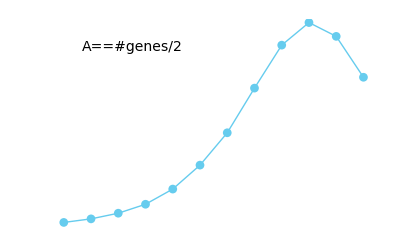

```mathematica
ListPlot[dat[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat],Style[#,12]&/@dat[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A=="#genes/2",14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_AhalfC",%]
```

progression_AhalfC.pdf